```mathematica
girr=Block[{x1={1,τ2+τ1,-1},x2={1,τ2,1},x3={1,τ3,1},x4={1,0,-1},U=2μ},
⟨SuperDagger[Subscript[c, x1]]·Subscript[c, x2]·SuperDagger[Subscript[c, x3]]·Subscript[c, x4]⟩-⟨SuperDagger[Subscript[c, x1]]·Subscript[c, x2]⟩⟨SuperDagger[Subscript[c, x3]]·Subscript[c, x4]⟩+⟨SuperDagger[Subscript[c, x1]]·Subscript[c, x4]⟩⟨SuperDagger[Subscript[c, x3]]·Subscript[c, x2]⟩]//F[#,τ2,β,ω2]&;
girr=girr/.ω2->Ω
```

-ⅇ^(-β μ-μ τ1+μ τ3)/((2+2 ⅇ^(-β μ))^2 (-2 μ+ⅈ Ω))+ⅇ^(-β μ-μ τ1+μ τ3+β (-2 μ+ⅈ Ω))/((2+2 ⅇ^(-β μ))^2 (-2 μ+ⅈ Ω))-ⅇ^(-β μ+μ τ1-μ τ3)/((2+2 ⅇ^(-β μ))^2 (2 μ+ⅈ Ω))+ⅇ^(-β μ+μ τ1-μ τ3+β (2 μ+ⅈ Ω))/((2+2 ⅇ^(-β μ))^2 (2 μ+ⅈ Ω))+(ⅈ ⅇ^(-μ τ1-μ τ3))/((2+2 ⅇ^(-β μ))^2 Ω)+(ⅈ ⅇ^(-2 β μ+μ τ1+μ τ3))/((2+2 ⅇ^(-β μ))^2 Ω)-(ⅈ ⅇ^(-μ τ1-μ τ3+ⅈ β Ω))/((2+2 ⅇ^(-β μ))^2 Ω)-(ⅈ ⅇ^(-2 β μ+μ τ1+μ τ3+ⅈ β Ω))/((2+2 ⅇ^(-β μ))^2 Ω)+(ⅈ ⅇ^(-μ (τ1+τ3)))/((2+2 ⅇ^(-β μ)) Ω)-(ⅈ ⅇ^(-μ (τ1+τ3)+ⅈ β Ω))/((2+2 ⅇ^(-β μ)) Ω)

```mathematica
g2irr[τ1_,τ3_,μ_,β_]=Limit[girr,Ω->0]//matsubara//Simplify
```

(ⅇ^(-μ (β+τ1+τ3)) (-ⅇ^(2 μ (β+τ1))+ⅇ^(2 μ (2 β+τ1))-ⅇ^(2 μ τ3)+ⅇ^(2 μ (β+τ3))+4 ⅇ^(2 β μ) β μ+6 ⅇ^(3 β μ) β μ+2 ⅇ^(μ (β+2 (τ1+τ3))) β μ))/(8 (1+ⅇ^(β μ))^2 μ)

```mathematica
Manipulate[
Plot3D[Evaluate@g2irr[τ1,τ3,μ,β],{τ1,0,β},{τ3,0,β},PlotRange->Full,AxesLabel->{"τ","τ'","g_(0, τ, τ')^(2  irr)"}],
{{μ,1},0,10},{{β,1},0,10}]
```

```mathematica
Plot3D[{g2irr[τ1,τ3,1,1],g2irr[2τ1,2τ3,1,2],g2irr[2.5τ1,2.5τ3,1,2.5]},{τ1,0,1},{τ3,0,1},PlotLegends->{"β=2.5","β=2","β=1"},PlotRange->Full,AxesLabel->{"τ","τ'","g_(0, τ, τ')^(2  irr)"},ColorFunction->Automatic,Ticks->{{{0,"0"},{1,"β"}},{{0,"0"},{1,"β"}}}]
```

-Graphics3D-

```mathematica
Block[{x1={1,τ1,1},x2={1,0,1},U=2μ},
⟨SuperDagger[Subscript[c, x1]]·Subscript[c, x2]⟩]//F[#,τ1,β,ω1]&//matsubara//Simplify
```

(ⅈ ω1)/(μ^2+ω1^2)

```mathematica
Clear[g];
g[ω_]:=(ⅈ ω)/(μ^2+ω^2)
G̃[ω_,{kx_,ky_}]:=1/(g[ω]-ϵ[kx,ky]^-1)
ϵ[kx_,ky_]:=2 t(Cos[kx]+Cos[ky])
```

```mathematica
x[β_,t_,μ_,Ω_,Kx_,Ky_,ω_]=G̃[ω,{kx,ky}]G̃[ω+Ω,{kx+Kx,ky+Ky}]-ϵ[kx,ky]ϵ[kx+Kx,ky+Ky]
```

-4 t^2 (Cos[kx]+Cos[ky]) (Cos[kx+Kx]+Cos[ky+Ky])+1/(((ⅈ ω)/(μ^2+ω^2)-1/(2 t (Cos[kx]+Cos[ky]))) ((ⅈ (ω+Ω))/(μ^2+(ω+Ω)^2)-1/(2 t (Cos[kx+Kx]+Cos[ky+Ky]))))

```mathematica
x[β_,t_,μ_,Ω_,n_,Kx_,Ky_,τ_]=G̃[ω,{kx,ky}]G̃[ω+Ω,{kx+Kx,ky+Ky}] ⅇ^(-ⅈ ω τ)/.ω->(2n+1)/β π
```

ⅇ^(-(ⅈ (1+2 n) π τ)/β)/(((ⅈ (1+2 n) π)/(β (((1+2 n)^2 π^2)/β^2+μ^2))-1/(2 t (Cos[kx]+Cos[ky]))) ((ⅈ (((1+2 n) π)/β+Ω))/(μ^2+(((1+2 n) π)/β+Ω)^2)-1/(2 t (Cos[kx+Kx]+Cos[ky+Ky]))))

```mathematica
1/(4 π^2)∫_-π^π ∫_-π^π ϵ[kx,ky]ϵ[kx+Kx,ky+Ky] ⅆkyⅆkx
```

2. t^2 (Cos[Kx]+Cos[Ky])

```mathematica
X[β_?NumberQ,t_?NumberQ,μ_?NumberQ,Ω_?NumberQ,n_?IntegerQ,Kx_?NumberQ,Ky_?NumberQ,τ_?NumberQ]:=NIntegrate[x[β,t,μ,Ω,n,Kx,Ky,τ],{kx,-π,π},{ky,-π,π}]
X[β_?NumberQ,t_?NumberQ,μ_?NumberQ,Ω_?NumberQ,Kx_?NumberQ,Ky_?NumberQ,ω_?NumberQ]:=NIntegrate[x[β,t,μ,Ω,Kx,Ky,ω],{kx,-π,π},{ky,-π,π}]
```

```mathematica
Manipulate[
Xτ=Sum[X[β,t,μ,Ω,Kx,Ky,(2n+1)/β π//N] ⅇ^(-ⅈ (2n+1)/β π τ)//N,{n,-15,15}];
Plot[Xτ//Re//Evaluate,{τ,-10,10},PlotRange->Full,AxesLabel->{"τ","X_(Ω, K, τ)^0"}]
,{{β,1},1,10},{{t,1},1,10},{{μ,1},1,10},{{Ω,0},0,10},{{Kx,0},-π,π},{{Ky,0},-π,π}
]
```

```mathematica
data=Table[Re[X[β,t,μ,Ω,Kx,Ky,ω//N]],{ω,(2(-50)+1)/β π,(2(50)+1)/β π,(2π)/β}];
```

```mathematica
Xτ1=Sum[X[β,1,1,0,0,0,(2n+1)/β π//N] ⅇ^(-ⅈ (2n+1)/β π τ)/.{β->1}//N,{n,-15,15}];
Xτ2=Sum[X[β,1,1,0,0,0,(2n+1)/β π//N] ⅇ^(-ⅈ (2n+1)/β π τ)/.{β->2}//N,{n,-15,15}];
Xτ3=Sum[X[β,1,1,0,0,0,(2n+1)/β π//N] ⅇ^(-ⅈ (2n+1)/β π τ)/.{β->2.5}//N,{n,-15,15}];
Xτ4=Sum[X[β,1,1,0,π,π,(2n+1)/β π//N] ⅇ^(-ⅈ (2n+1)/β π τ)/.{β->2.5}//N,{n,-15,15}];
Xτ5=Sum[X[β,1,1,10,0,0,(2n+1)/β π//N] ⅇ^(-ⅈ (2n+1)/β π τ)/.{β->2.5}//N,{n,-15,15}];
```

```mathematica
Xτ6=Sum[X[β,1,1,20,0,0,(2n+1)/β π//N] ⅇ^(-ⅈ (2n+1)/β π τ)/.{β->2.5}//N,{n,-15,15}];
```

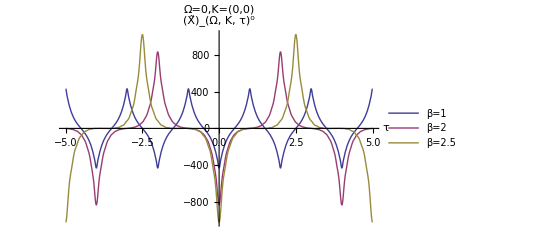

```mathematica
Plot[{Xτ1,Xτ2,Xτ3}//Re//Evaluate,{τ,-5,5},PlotRange->Full,PlotLabel->"Ω=0,K=(0,0)",AxesLabel->{"τ","(X̃)_(Ω, K, τ)^0"},PlotLegends->{"β=1","β=2","β=2.5"}]
```

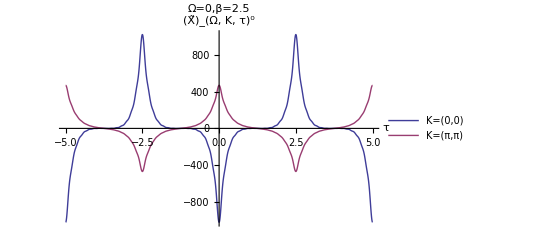

```mathematica
Plot[{Xτ3,Xτ4}//Re//Evaluate,{τ,-5,5},PlotRange->Full,PlotLabel->"Ω=0,β=2.5",AxesLabel->{"τ","(X̃)_(Ω, K, τ)^0"},PlotLegends->{"K=(0,0)","K=(π,π)"}]
```

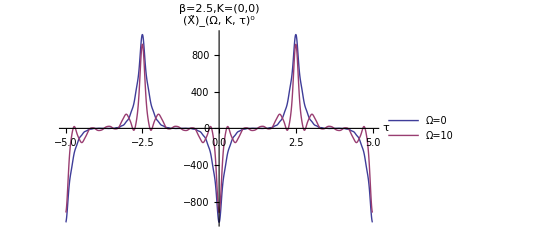

```mathematica
Plot[{Xτ3,Xτ5}//Re//Evaluate,{τ,-5,5},PlotRange->Full,PlotLabel->"β=2.5,K=(0,0)",AxesLabel->{"τ","(X̃)_(Ω, K, τ)^0"},PlotLegends->{"Ω=0","Ω=10"}]
```